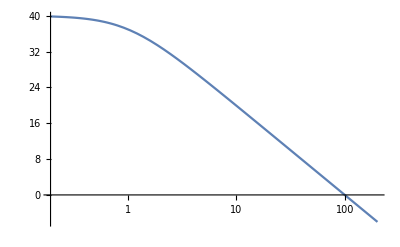

```mathematica
mag = LogLinearPlot[20*Log[10,100/Sqrt[1+( x)^2]],{x,0,200}]
```

```mathematica
SetDirectory["~/Desktop"]
```

/Users/niknejad/Desktop

```mathematica
Export["mag1pole.pdf",mag]
```

mag1pole.pdf

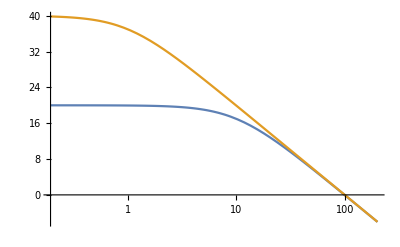

```mathematica
mag2 = LogLinearPlot[{20*Log[10,10/Sqrt[1+( x /10)^2]],20*Log[10,100/Sqrt[1+( x)^2]]},{x,0,200}]
```

```mathematica
Export["mag1pole_fb.pdf",mag2]
```

mag1pole_fb.pdf

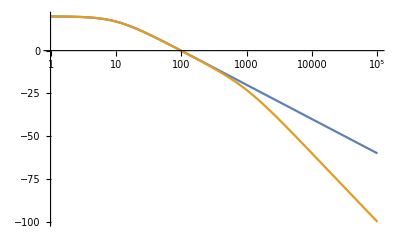

```mathematica
mag3 = LogLinearPlot[{20*Log[10,10/Sqrt[1+( .1 x )^2]],20*Log[10,10/(Sqrt[1+( .1 x)^2]Sqrt[1+( x /1000  )^2])]},{x,1,10^5}]
```

```mathematica
Export["mag2pole.pdf",mag3]
```

mag2pole.pdf

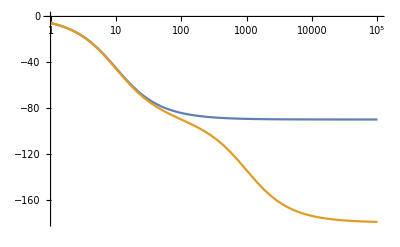

```mathematica
phase = LogLinearPlot[{-(180/Pi) ArcTan[.1 x], -(180/Pi) ArcTan[.1 x] - (180/Pi) ArcTan[ .001x]},{x,1,10^5}]
```

```mathematica
Export["phase2pole.pdf",phase]
```

phase2pole.pdf